## Select file

```mathematica
SetDirectory[NotebookDirectory[]];
$HistoryLength=2;
$Version
```

11.1.1 for Mac OS X x86 (64-bit) (April 18, 2017)

```mathematica
ClearAll[ncamString,ReadCenterFile,GetPositions,PredictAhead,PredictForward,PredictBackward,DoTracking,TryConnectingTracks,PreLabelList,ExportLabeledTracks]
ncamString[n_Integer]:=ncamString[n]=Join[{"Real32","Real32","Real32","Real32"},Join@@ConstantArray[{"UnsignedInteger8","UnsignedInteger16"},n]]
ReadCenterFile[fn_String]:=Module[{str,n,t,data,cams,other,alldata},
Print["Reading frames…"];
str=StringToStream[Import[fn,"String"]];
n=BinaryRead[str,"UnsignedInteger32"];
Print["Interpreting data…"];
t=0;
alldata=Reap[
While[n=!=EndOfFile∧t<9999999,
data=Table[
cams=BinaryRead[str,"UnsignedInteger8"];
If[cams==EndOfFile,
Print[fn];
Print[n];
Break[];
];
other=ncamString[cams];
(*other=BinaryRead[str,other];*)
other=BinaryReadList[str,other,1];
Prepend[other[[1]],cams]
,
{n}
];
Sow[data];
n=BinaryRead[str,"UnsignedInteger32"] (* for next frame *)
]
][[2,1]];
Close[str];
alldata
]
GetPositions[alldata_List,n_Integer]:=Module[{},
If[n<=Length[alldata],
alldata[[n,All,2;;4]]
,
{}
]
]
PredictAhead[{}]:={}
PredictAhead[l:{_}]:=First[l]
PredictAhead[l_List]:=2l[[-1]]-l[[-2]]
PredictForward[{penultimate_,last_}]:=2last-penultimate
PredictBackward[{first_,second_}]:=2first-second
TryConnectingTracks[trackstorage_List,connectcutoff_]:=Module[{ts,its,future,past,validoptions,fut,pas,dm,poss,options,usedfuture,usedpast,components,delindex},
ts=trackstorage;
Print["Calculating and future and paste points…"];
ts=SortBy[ts,#[[1,1]]&];
its={Range[Length[ts]],ts}ᵀ;
future={#1,#2[[-1,1]]+1,PredictForward[#2[[-2;;,3]]],#2[[-1,3]]-#2[[-2,3]]}&@@@its; (* trackid, time, point, direction of particle *)
past={#1,#2[[1,1]]-1,PredictBackward[#2[[;;2,3]]],#2[[2,3]]-#2[[1,3]]}&@@@its;
Print["Grouping by time-stamp…"];
future=GroupBy[future,#[[2]]&->Delete[2]];
past=GroupBy[past,#[[2]]&->Delete[2]];
{future,past}=KeyIntersection[{future,past}];

Print["Finding possible candidates…"];
validoptions={};
Do[
fut=future[t];
pas=past[t];
dm=DistanceMatrix[fut[[All,2]],pas[[All,2]]];
poss=Position[dm,_?(LessThan[connectcutoff]),{2}];
options={fut[[#1]],pas[[#2]]}&@@@poss;
options={First[#1],First[#2],Norm[#1[[2]]-#2[[2]]],VectorAngle[#1[[3]],#2[[3]]]}&@@@options;
options=Select[options,Last[#]<20.0Degree&];
options=SortBy[options,Last];

usedfuture=<||>;
usedpast=<||>;
Do[
If[!KeyExistsQ[usedfuture,c[[1]]],
If[!KeyExistsQ[usedpast,c[[2]]],
AssociateTo[usedfuture,c[[1]]->1];
AssociateTo[usedpast,c[[2]]->1];
AppendTo[validoptions,c];
]
]
,
{c,options}
];
,
{t,Keys[future]}
];
Print["Connections found: ",Length[validoptions]];
components=Sort/@WeaklyConnectedComponents[DirectedEdge@@@validoptions[[All,;;2]]];
Print["Length of track combinations: ",Tally[Length/@components]];
Print["Combining tracks…"];
Do[
ts[[First[c]]]=Join@@ts[[c]]
,
{c,components}
];
delindex=Join@@(Rest/@components);
ts=Delete[ts,List/@delindex];
ts
]
PreLabelList[list_List,label_]:=Map[Prepend[label],list]
ExportLabeledTracks[fnout_String,labeledtracks_List]:=Module[{trackout,tmpout,str},
tmpout=CreateFile[];
trackout=Flatten@labeledtracks;
str=OpenWrite[tmpout,BinaryFormat->True];
BinaryWrite[str,trackout,{"UnsignedInteger32","UnsignedInteger16","UnsignedInteger16","Real32","Real32","Real32"}] (* trackid, time, original ID, x, y, z *);
Close[str];
CopyFile[tmpout,fnout];
DeleteFile[tmpout];
]
DoTracking[fn_String,fnout_String, cutoff_:0.2,minimumtracklength:_Integer:8]:=Module[{alldata,start,elapsed,elapsed2,elapsed3,trackstorage,maxtime,t,tracks,lasttracks,newpts,cands,additions,usedtracks,usednewpts,itracks,inewpts,add,unusedtrackids,unusednewptsids,trackout},
start=AbsoluteTime[];
alldata=ReadCenterFile[fn];
elapsed=AbsoluteTime[]-start;
Print["Reading ",Length[alldata]," frames took: ",elapsed," sec. Or ",elapsed/Length[alldata]," sec/frame."];

Print["Starting matching…"];
start=AbsoluteTime[];
trackstorage = {};
maxtime=Length[alldata];
t=1;
tracks=MapIndexed[{{t,#2[[1]],#1}}&,GetPositions[alldata,t]]; (* label first points as start of new tracks*)

Do[
t+=1;
lasttracks = PredictAhead/@tracks[[All,All,3]]; (* if the track is length >1 then predict based on velocity *)
newpts=GetPositions[alldata,t];
If[Length[lasttracks]>0,
cands =MapThread[Prepend[#2]/@ #1&,{Nearest[lasttracks->{"Index","Distance"},newpts,{All,cutoff}],Range[Length[newpts]]}];
cands=SortBy[Join@@cands,Last][[All,;;2]];
,
cands={};
];
additions={};
usedtracks=<||>;
usednewpts = <||>;

(* select best matches and keep track of which ones are matched *)
Do[
If[!KeyExistsQ[usedtracks,c[[1]]],
If[!KeyExistsQ[usednewpts,c[[2]]],
AssociateTo[usedtracks,c[[1]]->1];
AssociateTo[usednewpts,c[[2]]->1];
AppendTo[additions,c]
]
]
,
{c,cands}
];

(* make active tracks longer *)
Do[
{inewpts,itracks}=add;
AppendTo[tracks[[itracks]],{t,inewpts,newpts[[inewpts]]}]
,
{add,additions}
];

(* which tracks are not enlarged, and which points are not used *)
unusedtrackids=Complement[Range[Length[tracks]],additions[[All,2]]];
unusednewptsids = Complement[Range[Length[newpts]],additions[[All,1]]];

(* tracks that are not appended permanently store them, but only if they have minimum length*)
trackstorage=Join[trackstorage,Select[tracks[[unusedtrackids]],Length[#]>=minimumtracklength&]];
tracks=Delete[tracks,List/@unusedtrackids]; (* delete from active tracks*)

(* unused particles will form new tracks: *)
tracks=Join[tracks,MapIndexed[{{t,#2[[1]],#1}}&,newpts[[unusednewptsids]]]];
,
{maxtime-1}
];
trackstorage=Join[trackstorage,Select[tracks,Length[#]>=minimumtracklength&]];
elapsed2=AbsoluteTime[]-start;
Print["That took: ",elapsed2," sec. Or ",elapsed2/maxtime," sec/frame."];

start=AbsoluteTime[];
trackstorage=TryConnectingTracks[trackstorage,cutoff/2.0];
elapsed3=AbsoluteTime[]-start;
Print["That took: ",elapsed3," sec. Or ",elapsed3/maxtime," sec/frame."];
Print["Total time: ",elapsed + elapsed2+elapsed3," sec. Or ",(elapsed + elapsed2+elapsed3)/maxtime," sec/frame."];
Print[Length[trackstorage]," tracks."];

trackout=SortBy[trackstorage,{#[[1,1]]&,#[[-1,1]]&}];
trackout=MapIndexed[PreLabelList[#1,First[#2]]&,trackout];
If[True,
ExportLabeledTracks[fnout,trackout];
Print["Exporting done to: ",fnout];
,
trackout
]
]
```

## Area 51

```mathematica
fns=FileNames["matched_*.dat",NotebookDirectory[],∞]
fns//Length

out=ReadCenterFile[fns[[1]]];

bb=CoordinateBounds[Join@@out[[All,All,2;;4]]];
Manipulate[Graphics3D[Point[out[[n,All,2;;4]]],PlotRange->bb],{n,1,500,1}]
```

```mathematica
trackz=DoTracking[fns[[3]],"bla.dat", 0.2,8];
```

Reading frames…

Interpreting data…

Reading 3200 frames took: 11.98257 sec. Or 0.003744554 sec/frame.

Starting matching…

That took: 6.89814 sec. Or 0.002155669 sec/frame.

Calculating and future and paste points…

Grouping by time-stamp…

Finding possible candidates…

Connections found: 6

Length of track combinations: {{2,6}}

Combining tracks…

That took: 0.638352 sec. Or 0.000199485 sec/frame.

Total time: 19.51907 sec. Or 0.006099708 sec/frame.

2205 tracks.

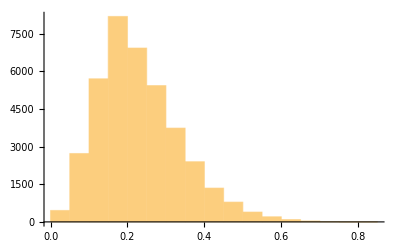

```mathematica
(*long=Select[trackz,Length[#]>30&];*)
long=trackz;
long=long[[All,All,4]];
long=Differences/@long;
long=Join@@Map[Norm,long,{2}];
Histogram[long]
```

### AG 0

```mathematica
Quantile[long,0.75]
```

0.228962

### AG 0.2

```mathematica
Quantile[long,0.75]
```

0.247184

### AG 1.0

```mathematica
Quantile[long,0.75]
```

0.293939

### AG Plot

FittedModel[0.230762+0.0639286 x]

0.230762+0.0639286 #1&

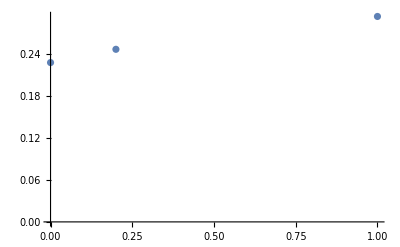

```mathematica
data={{0,0.228},{0.2,0.247},{1.0,0.294}};
fit=LinearModelFit[data,{1,x},x]
fit=fit["Function"]
ListPlot[data,PlotRange->{{0,All},{0,All}}]
```

## ALL: 0.3 mm (much smaller than particle size)

```mathematica
fns=FileNames["rays_*cpp.bin",NotebookDirectory[],∞];
fns=Select[fns,StringContainsQ["rays_MF_18.5_AG_0_Surf_4_out_cpp.bin"]];
fns//Length
fnout=fns
fnout//Length
fnout=StringReplace[fnout,{"rays"->"tracked","_out_cpp.bin"->".dat"}];

CloseKernels[];
LaunchKernels[4];
DistributeDefinitions[fnout,fns,DoTracking]

ParallelDo[
If[!FileExistsQ[fnout[[i]]]∧fnout[[i]]=!=fns[[i]],
Print["Doing ", fns[[i]],"…"];
DoTracking[fns[[i]],fnout[[i]],0.4,8];
,
Print[fnout[[i]], " exists already!"];
]
,
{i,Length[fns]}
,
Method->"FinestGrained"
]
```

1

{/Users/sanderhuisman/Desktop/TwenteBB/Data/TwenteBubbles2/AG_0/rays_MF_18.5_AG_0_Surf_4_out_cpp.bin}

1

{fnout,fns,DoTracking,ReadCenterFile,ncamString,GetPositions,PredictAhead,TryConnectingTracks,PredictForward,PredictBackward,PreLabelList,ExportLabeledTracks}

Doing /Users/sanderhuisman/Desktop/TwenteBB/Data/TwenteBubbles2/AG_0/rays_MF_18.5_AG_0_Surf_4_out_cpp.bin…

Reading frames…

Interpreting data…

Reading 3200 frames took: 14.62207 sec. Or 0.004569396 sec/frame.

Starting matching…

That took: 9.309211 sec. Or 0.002909128 sec/frame.

Calculating and future and paste points…

Grouping by time-stamp…

Finding possible candidates…

Connections found: 83

Length of track combinations: {{3,2},{2,79}}

Combining tracks…

That took: 0.827731 sec. Or 0.000258666 sec/frame.

Total time: 24.75901 sec. Or 0.007737191 sec/frame.

3679 tracks.

Exporting done to: /Users/sanderhuisman/Desktop/TwenteBB/Data/TwenteBubbles2/AG_0/tracked_MF_18.5_AG_0_Surf_4.dat